```mathematica
u=(√(-π τ))/2 HankelH1[ν,-k τ]
ϕ=u/(-1/H/τ)
uc=(√(-π τ))/2 HankelH2[ν,-k τ]
ϕc=uc/(-1/H/τ)
```

1/2 √π √-τ HankelH1[ν,-k τ]

-1/2 H √π √-τ τ HankelH1[ν,-k τ]

1/2 √π √-τ HankelH2[ν,-k τ]

-1/2 H √π √-τ τ HankelH2[ν,-k τ]

```mathematica
-1/2 H √π √-τ τ HankelH2[ν,-k τ]
```

-1/2 H √π √-τ τ HankelH2[ν,-k τ]

```mathematica
dϕ= D[ϕ, τ]
dϕc = D[ϕc, τ]
```

-1/2 H √π √-τ HankelH1[ν,-k τ]+(H √π τ HankelH1[ν,-k τ])/(4 √-τ)+1/4 H k √π √-τ τ (HankelH1[-1+ν,-k τ]-HankelH1[1+ν,-k τ])

-1/2 H √π √-τ HankelH2[ν,-k τ]+(H √π τ HankelH2[ν,-k τ])/(4 √-τ)+1/4 H k √π √-τ τ (HankelH2[-1+ν,-k τ]-HankelH2[1+ν,-k τ])

## Phi v Real & Imaginary Integrals

```mathematica
subs={H->1,σ->0.01,δ->0.5,ν->1};
```

```mathematica
u=Sqrt[-π τ]/2 HankelH1[ν,-k τ];
ϕ=u/(-1/H/τ);
uc=Sqrt[-π τ]/2 HankelH2[ν,-k τ];
ϕc=uc/(-1/H/τ);

dϕ=D[ϕ,τ];
dϕc=D[ϕc,τ];

subs={H->1,σ->0.01,δ->0.5,ν->1};

Plot3D[Abs[Re[NIntegrate[k^4 τ1 τ2 (ϕ/. {τ->τ1}/. subs) (dϕc/. {τ->τ2}/. subs),{k,(-((1-δ) σ)/τ2)/. subs,(-((1+δ) σ)/τ1)/. subs}]]],{τ1,-1,-0.1},{τ2,-1,-0.1},RegionFunction->Function[{τ1,τ2,z},(τ1<τ2<0)&&(τ2/τ1>((1-δ)/(1+δ)/. subs))],AxesLabel->{"τ1","τ2","C"},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Abs[Im[NIntegrate[k^4 τ1 τ2 (ϕ/. {τ->τ1}/. subs) (dϕc/. {τ->τ2}/. subs),{k,(-((1-δ) σ)/τ2)/. subs,(-((1+δ) σ)/τ1)/. subs}]]],{τ1,-1,-0.1},{τ2,-1,-0.1},RegionFunction->Function[{τ1,τ2,z},(τ1<τ2<0)&&(τ2/τ1>((1-δ)/(1+δ)/. subs))],AxesLabel->{"τ1","τ2","C"},PlotRange->All]
```

-Graphics3D-

```mathematica
(* ===Definitions (must run first,every session)===*)Clear[u,ϕ,uc,ϕc,dϕ,dϕc,τ,k,τ1,τ2];

u=Sqrt[-π τ]/2 HankelH1[ν,-k τ];
ϕ=u/(-1/H/τ);
uc=Sqrt[-π τ]/2 HankelH2[ν,-k τ];
ϕc=uc/(-1/H/τ);
dϕ=D[ϕ,τ];
dϕc=D[ϕc,τ];

subs={H->1,σ->0.01,δ->0.5,ν->1};

(* ===Sanity check before running the full plot===*)
ϕ/. {τ->-0.5}/. subs
dϕc/. {τ->-0.3}/. subs
```

0.313329 HankelH1[1,0.5 k]

-0.72811 HankelH2[1,0.3 k]-0.072811 k (HankelH2[0,0.3 k]-HankelH2[2,0.3 k])

```mathematica
subs={H->1,σ->0.01,δ->0.5,ν->1.5};(* ===Classicality plot===*)Plot3D[Module[{integral,kmin,kmax,re,im},kmin=N[(-((1-δ) σ)/τ2)/. subs];
kmax=N[(-((1+δ) σ)/τ1)/. subs];
integral=NIntegrate[k^4 τ1 τ2 (ϕ/. {τ->τ1}/. subs) (dϕc/. {τ->τ2}/. subs),{k,kmin,kmax}];
re=Re[integral];
im=Im[integral];
If[Abs[im]<10^-12,Indeterminate,Abs[re/im]]],{τ1,-1,-0.1},{τ2,-1,-0.1},RegionFunction->Function[{τ1,τ2,z},(τ1<τ2<0)&&(τ2/τ1>N[((1-δ)/(1+δ)/. subs)])],AxesLabel->{"τ1","τ2","Classicality"},PlotRange->All,PlotPoints->25,MaxRecursion->1]
```

-Graphics3D-

```mathematica
ConfigureMaTeX["Ghostscript"->"C:/Program Files/gs/gs10.07.1/bin/gswin64c.exe"]
```

{pdfLaTeX→C:\Users\Melika\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,CacheSize→100,WorkingDirectory→Automatic,Ghostscript→C:/Program Files/gs/gs10.07.1/bin/gswin64c.exe}

```mathematica
{"pdfLaTeX"->"C:\\Users\\Melika\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe","CacheSize"->100,"WorkingDirectory"->Automatic,"Ghostscript"->"C:/Program Files/gs/gs10.07.1/bin/gswin64c.exe"}
```

{pdfLaTeX→C:\Users\Melika\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,CacheSize→100,WorkingDirectory→Automatic,Ghostscript→C:/Program Files/gs/gs10.07.1/bin/gswin64c.exe}

```mathematica
Needs["MaTeX`"]
```

```mathematica
subs={H->1,σ->0.01,δ->0.5,ν->1.49};(* ===Classicality plot===*)Plot3D[Module[{integral,kmin,kmax,re,im},kmin=N[(-((1-δ) σ)/τ2)/. subs];
kmax=N[(-((1+δ) σ)/τ1)/. subs];
integral=NIntegrate[k^4 τ1 τ2 (ϕ/. {τ->τ1}/. subs) (dϕc/. {τ->τ2}/. subs),{k,kmin,kmax}];
re=Re[integral];
im=Im[integral];
If[Abs[im]<10^-12,Indeterminate,Abs[re/im]]],{τ1,-1,-0.1},{τ2,-1,-0.1},RegionFunction->Function[{τ1,τ2,z},(τ1<τ2<0)&&(τ2/τ1>N[((1-δ)/(1+δ)/. subs)])],AxesLabel->{MaTeX["\\tau_1"],MaTeX["\\tau_2"],MaTeX["\\mathrm{C_{\\phi v}}"]},PlotRange->All,PlotPoints->25,MaxRecursion->1]
```

-Graphics3D-

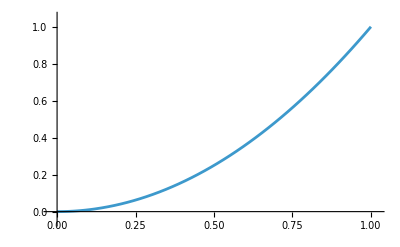

```mathematica
Plot[x^2,{x,0,1}]
```

```mathematica
(*3 Tir*)
```

```mathematica
subs={H->1,σ->0.01,δ->0.5,ν->1.49};
```

```mathematica
gv[τ1_,τ2_]:=gv[τ1,τ2]=Module[{kmin,kmax},kmin=N[(-((1-δ) σ)/τ2)/. subs];
kmax=N[(-((1+δ) σ)/τ1)/. subs];
NIntegrate[k^4 τ1 τ2 (ϕ/.{τ->τ1}/.subs) (dϕc/.{τ->τ2}/.subs),{k,kmin,kmax},Method->{"GlobalAdaptive","SingularityHandler"->"IMT"},AccuracyGoal->8,PrecisionGoal->6,MaxRecursion->20]];
```

```mathematica
(*5 Tir*)
```

```mathematica
(*7 Tir*)
```

```mathematica
subs={H->1,σ->0.01,δ->0.5,ν->1};(* ===Classicality plot===*)Plot3D[Module[{integral,kmin,kmax,re,im},kmin=N[(-((1-δ) σ)/τ2)/. subs];
kmax=N[(-((1+δ) σ)/τ1)/. subs];
integral=NIntegrate[k^4 τ1 τ2 (ϕ/. {τ->τ1}/. subs) (dϕc/. {τ->τ2}/. subs),{k,kmin,kmax}];
re=Re[integral];
im=Im[integral];
If[Abs[im]<10^-12,Indeterminate,Abs[re/im]]],{τ1,-1,-0.1},{τ2,-1,-0.1},RegionFunction->Function[{τ1,τ2,z},(τ1<τ2<0)&&(τ2/τ1>N[((1-δ)/(1+δ)/. subs)])],AxesLabel->{"τ1","τ2","Classicality"},PlotRange->All,PlotPoints->25,MaxRecursion->1]
```

-Graphics3D-

```mathematica
(*----Step 1:define the massive mode functions (global ϕ,dϕc with ν as a parameter)----*)ϕ[τ_,ν_]:=-(1/2) H Sqrt[π] Sqrt[-τ] τ HankelH1[ν,-k τ];

dϕc[τ_,ν_]:=-(1/2) H Sqrt[π] Sqrt[-τ] HankelH2[ν,-k τ]+(H Sqrt[π] τ HankelH2[ν,-k τ])/(4 Sqrt[-τ])+1/4 H k Sqrt[π] Sqrt[-τ] τ (HankelH2[-1+ν,-k τ]-HankelH2[1+ν,-k τ]);

(*----Step 2:a memoized classicality function,parametrized by ν----*)
ClearAll[classicality];
classicality[τ1_?NumericQ,τ2_?NumericQ,νval_?NumericQ]:=classicality[τ1,τ2,νval]=Module[{subs,kmin,kmax,integral,re,im},subs={H->1,σ->0.01,δ->0.5};
kmin=N[(-((1-δ) σ)/τ2)/. subs];
kmax=N[(-((1+δ) σ)/τ1)/. subs];
integral=NIntegrate[k^4 τ1 τ2 ϕ[τ1,νval] dϕc[τ2,νval]/. subs,{k,kmin,kmax},Method->{"GlobalAdaptive","SingularityHandler"->"IMT"},AccuracyGoal->8,PrecisionGoal->8,MaxRecursion->10];
re=Re[integral];im=Im[integral];
If[Abs[im]<10^-12,Indeterminate,Abs[re/im]]];

(*----Step 3:build the RegionFunction once (depends only on δ,not ν)----*)
regFn=Function[{τ1,τ2,z},(τ1<τ2<0)&&(τ2/τ1>N[(1-0.5)/(1+0.5)])];

(*----Step 4:precompute Plot3D for a grid of ν values----*)
νvalues=Range[1,2,0.05];  (*adjust range/step to taste,include 1.5 explicitly if you want it*)

plotAssoc=Association[];
Do[Print["Computing ν = ",νval];
plotAssoc[νval]=Plot3D[classicality[τ1,τ2,νval],{τ1,-1,-0.1},{τ2,-1,-0.1},RegionFunction->regFn,AxesLabel->{"τ1","τ2","Classicality"},PlotRange->All,PlotPoints->25,MaxRecursion->1],{νval,νvalues}]

(*----Step 5:Manipulate just looks up the nearest precomputed plot----*)
Manipulate[plotAssoc[Nearest[νvalues,νselect][[1]]],{{νselect,1.5,"ν"},1,2,0.05,Appearance->"Labeled"}]
```

SetDelayed::write: Tag Times in (-1/2 H √π √-τ τ HankelH1[ν,-k τ])[τ_,ν_] is Protected.

SetDelayed::write: Tag Plus in (-1/2 H √π √-τ HankelH2[ν,-k τ]+(H √π τ HankelH2[ν,-k τ])/(4 √-τ)+1/4 H k √π √-τ τ (HankelH2[-1+ν,-k τ]-HankelH2[1+ν,-k τ]))[τ_,ν_] is Protected.

Computing ν = 1.

NIntegrate::inumr: The integrand 0.999925 k^4 (-1/2 √π √-τ τ HankelH1[ν,-k τ])[-0.999962,1.] (-1/2 √π √-τ HankelH2[ν,-k τ]+(√π τ HankelH2[ν,-k τ])/(4 √-τ)+1/4 k √π √-τ τ (HankelH2[-1+ν,-k τ]-HankelH2[1+ν,-k τ]))[-0.999962,1.] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.00500019,0.0150006}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Computing ν = 1.05

Computing ν = 1.1

Computing ν = 1.15

Computing ν = 1.2

Computing ν = 1.25

Computing ν = 1.3

Computing ν = 1.35

Computing ν = 1.4

Computing ν = 1.45

Computing ν = 1.5

Computing ν = 1.55

Computing ν = 1.6

Computing ν = 1.65

Computing ν = 1.7

Computing ν = 1.75

Computing ν = 1.8

Computing ν = 1.85

Computing ν = 1.9

Computing ν = 1.95

Computing ν = 2.

Nearest::near1: 
   νvalues is neither a list of real points nor a valid list of rules.

Nearest::near1: νvalues is neither a list of real points nor a valid list of rules.

Nearest::near1: 
   νvalues is neither a list of real points nor a valid list of rules.

Nearest::near1: νvalues is neither a list of real points nor a valid list of rules.

Nearest::near1: 
   νvalues is neither a list of real points nor a valid list of rules.

```mathematica
(*8 Tir*)
subs={H->1,σ->0.01,δ->0.5,ν->1.49};
Plot3D[Module[{kmin,kmax,integral,re,im},kmin=Min[-(((1-δ) σ)/τ2),-(((1+δ) σ)/τ1)]/. subs;
kmax=Max[-(((1-δ) σ)/τ2),-(((1+δ) σ)/τ1)]/. subs;
integral=NIntegrate[k^4 τ1 τ2 (ϕ/. {τ->τ1}) (ϕc/. {τ->τ2})/. subs,{k,kmin,kmax}];
re=Re[integral];im=Im[integral];
If[Abs[im]<10^-12,Indeterminate,Abs[re/im]]],{τ1,-1,-0.1},{τ2,-1,-0.1},RegionFunction->Function[{τ1,τ2,z},(τ1<0)&&(τ2<0)&&(Max[τ1,τ2]/Min[τ1,τ2]<((1+δ)/(1-δ))/. subs)],AxesLabel->{"τ1","τ2","C"},PlotRange->{0,1000}]
```

-Graphics3D-

```mathematica
(*13 Tir--------------------------------------------------------------------------------------------------------*)
baseSubs={H->1,σ->0.01,δ->0.5};

ClearAll[g];
g[τ1_?NumericQ,τ2_?NumericQ,νval_?NumericQ]:=g[τ1,τ2,νval]=Module[{subs,kmin,kmax,integral,re,im},subs=Join[baseSubs,{ν->νval}];
kmin=N[(-((1-δ) σ)/τ2)/. subs];
kmax=N[(-((1+δ) σ)/τ1)/. subs];
integral=NIntegrate[k^4 τ1 τ2 (ϕ/. {τ->τ1}/. subs) (dϕc/. {τ->τ2}/. subs),{k,kmin,kmax}];
re=Re[integral];im=Im[integral];
If[Abs[im]<10^-12,Indeterminate,Abs[re/im]]];

classicalityPlot[νval_?NumericQ]:=Plot3D[g[τ1,τ2,νval],{τ1,-1,-0.1},{τ2,-1,-0.1},RegionFunction->Function[{τ1,τ2,z},(τ1<τ2<0)&&(τ2/τ1>N[((1-δ)/(1+δ))/. baseSubs])],AxesLabel->{"τ1","τ2","Classicality"},PlotRange->All,PlotPoints->25,MaxRecursion->1,PlotLabel->"ν = "<>ToString[νval]]

(*Now just sweep values:*)
νlist={1.49,1.499,1.4999,1.5};
plots=classicalityPlot/@νlist;
GraphicsGrid[Partition[plots,2],ImageSize->900]
```

-Graphics-